```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = (w*bPred*P*C +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[M],bPredSub->bPredSub[M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+w*b*P)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],b->b[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC,0==eqnR},{P,C,R}]];
```

```mathematica
Psol = P/.LVSS[[5]]
Csol = C/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[M])/w-(8 μ[M])/w+((-3 √kRes √w √α √bPred[M] √Y[M]+√(9 kRes w α bPred[M] Y[M]-16 λ[M] (Sub (-1+w) bPredSub[M]+μPred[M]))) (kRes w α bPred[M] Y[M]+2 (Sub (-1+w) bPredSub[M]+μPred[M]) σ[M]))/(√kRes w^(3/2) √α √bPred[M] √Y[M] (Sub (-1+w) bPredSub[M]+μPred[M])))/(8 b[M])

(Sub (-1+w) bPredSub[M]+μPred[M])/(w bPred[M])

kRes/4+(√kRes √(9 kRes w α bPred[M] Y[M]-16 λ[M] (Sub (-1+w) bPredSub[M]+μPred[M])))/(4 √w √α √bPred[M] √Y[M])

```mathematica
PsolNoSubsidies= Psol/.w->1
CsolNoSubsidies= Csol/.w->1
```

(8 λ[M]-8 μ[M]+((-3 √kRes √α √bPred[M] √Y[M]+√(9 kRes α bPred[M] Y[M]-16 λ[M] μPred[M])) (kRes α bPred[M] Y[M]+2 μPred[M] σ[M]))/(√kRes √α √bPred[M] √Y[M] μPred[M]))/(8 b[M])

μPred[M]/bPred[M]

```mathematica
CsolAllSubsidies = Limit[Csol/.Sub->10,w->0]
```

Indeterminate

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C],D[eqnP,R]},
{D[eqnC,P],D[eqnC,C],D[eqnC,R]},
{D[eqnR,P],D[eqnR,C],D[eqnR,R]}})/.{P->Psol,C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ExpPredfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps.csv"}],"csv"];
ExpPredmassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPredmass_tablereps.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
(*OptPredMass[M_]:=ppmrint*M^ppmrslope;*)

(*A Piecewise function incorporate a) the Cruz/Pires relationship for Prey masses 5-10^4 grams; b) the Hayward relationship fro 10^4-10^7 grams*)
breakpoint = 10^4;
(*OptPredMass[M_] := Piecewise[{{Exp[3.5]*M,M<breakpoint},{ppmrint*M^ppmrslope,M>=breakpoint}}];*)
OptPredMass[M_] := ppmrint*M^ppmrslope;
ppmrslope = (ExpPredfitdata[[3,1]]);
ppmrint = Exp[(ExpPredfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
(*OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];*)
```

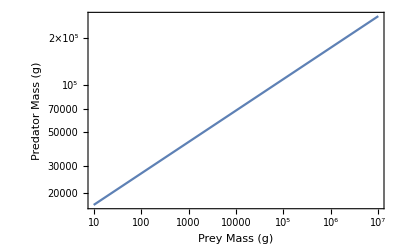

```mathematica
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16]]
```

```mathematica
OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
(*predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];*)
(*predatedconsumerdensity[Mp_,M_]:=1/Ypred[Mp,M];*)
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*1/Ypred[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];
b[M_] :=predmortalityfull[OptPredMass[M],M];

predgrowth =  FullSimplify[predgrowthrateperconsumer[Mp,M]]; (*predatedconsumerdensity without the 1/Yield*)
predgrowthfull[Mp_,M_]:=Evaluate[predgrowth//Simplify];
bPred[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPred[M_]:=λPred[OptPredMass[M]];*)
(*bPredSub[M_]:=predgrowthfull[OptPredMass[M],M];*)
bPredSub[M_]:=Sub*λPred[OptPredMass[M]];



(*Predator starvation*)
σPred[M_]:=(1/τsig [OptPredMass[M]]);
kCons[M_]:=PreyDensityTheoreticalMax[M]; (*Consumer theroetical maximum*)
(*Predator mortality*)
μPred[M_] := (a0*(Exp[a1*a2*OptPredMass[M]^(b1+b2)]-1)*OptPredMass[M]^(b0-b1-b2))/(a1*a2);   (* this is the consumer death rate*)
(*Subsidies could be set as mass dependent or mass-independent*)
(*Sub[M_]:=CsolNoSubsidies;*)
```

```mathematica
(*AverageCsolDensity=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];
Sub = ϵ*AverageCsolDensity;*)
Sub = ϵ*1;
```

```mathematica
Sub
```

ϵ

```mathematica
Esub = Integrate[(1/M)*Eprey[M],{M,1,10^7}]
```

459825.

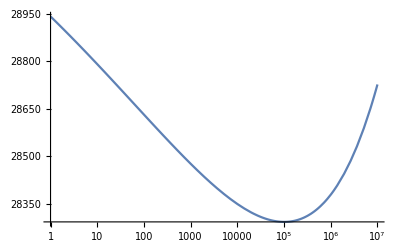

```mathematica
LogLinearPlot[Eprey[M],{M,1,10^7}]
```

```mathematica
Esub=Mean[Table[Eprey[M]/.M->10^i,{i,1,7,0.0001}]]
```

28472.1

```mathematica
(*Sub=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];*)(*1*)(*0.1*CsolNoSubsidies;*)
```

```mathematica
(*SubDensity=10*Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]]*)
```

Show the inputted PPMR

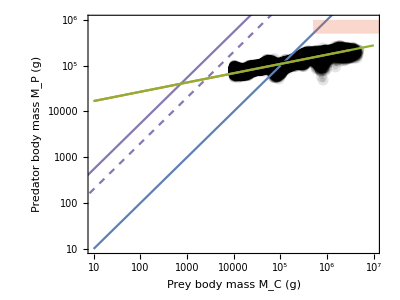

```mathematica
nlm = NonlinearModelFit[ExpPredmassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000];
lm =LinearModelFit[Log@(ExpPredmassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95];
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[ExpPredmassdata*1000,Frame->True,FrameLabel->{"Prey body mass M_C (g)","Predator body mass M_P (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^1,1*10^7},{10^1,10^6}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]],
LogLogPlot[Exp[4]*M,{M,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4]
```

Calculate Intersection of Cruz/Pires relationship and Hayward relationship

```mathematica
(Exp[3.5]/ppmrint)^(1/(ppmrslope-1))
```

1382.67

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

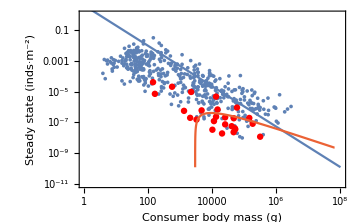

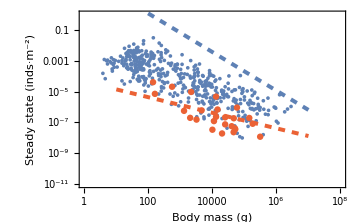

```mathematica
PercentGrowthConsumer=0.8; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidy =0.01;
PCDensityPlot=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf"}],PCDensityPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf

1584.89

52484.5

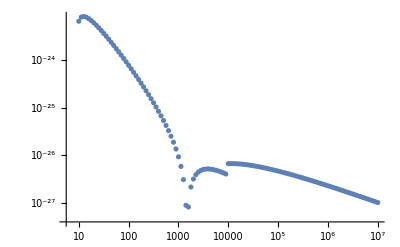

```mathematica
detlist = ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->1,Sub->1}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]
```

Now look at results WITH SUBSIDIES

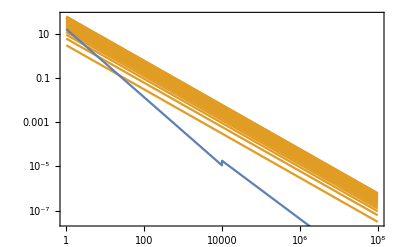

```mathematica
Show[{
LogLogPlot[{Table[(1/M)*Sub/.{ϵ->i},{i,0.1,2,0.1}]},{M,1,10^8},PlotStyle->ColorData[97,2],Frame->True],
LogLogPlot[(1/M)*CsolNoSubsidies,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

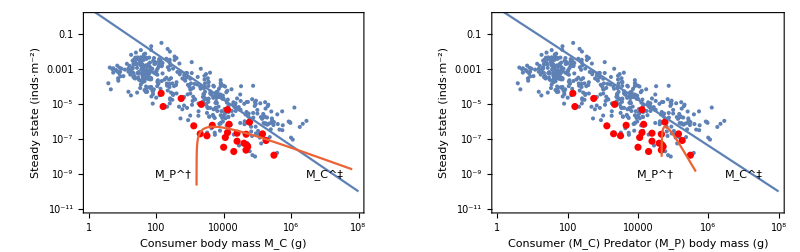

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
PredDensityList=Table[{10^i,((1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.M->10^i},{i,1,8,0.01}];
PredDensityListPredMass = Transpose[{OptPredMass[PredDensityList[[All,1]]],PredDensityList[[All,2]]}];
ThresholdPopulationPlot=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]],
Graphics[{Text["M_P^†",{Log@(10^2.5),Log@(10^(-9))}]}],
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
(*LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]*)
ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]],
Graphics[{Text["M_P^†",{Log@(10^4.5),Log@(10^(-9))}]}],
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]
}]
},ImageSize->800]
(*MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]*)
```

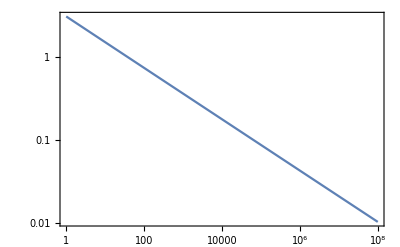

```mathematica
LogLogPlot[Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
```

```mathematica
Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue,M->50000}
```

0.106882

```mathematica
DensityList=Table[{10^i,((1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})M->10^i},{i,1,8,0.01}];
DensityListPredMass = Transpose[{OptPredMass[DensityList[[All,1]]],DensityList[[All,2]]}];
```

Evaluate the herbivore and predator body size thresholds across different values of w and Sub

```mathematica
iterator = 0.1;
ThresholdsOverWEpsilon=Flatten[ParallelTable[
(*PreySSMin=M/.N[(FindMinimum[{Abs[(1/M)*Csol/.{w->wvalues,ϵ->epsilonvalues}],{M>10001 &&M<10^8}},{M}])][[2]];
PredSSMin=M/.N[(FindMinimum[{Abs[(1/M)*Psol/.{w->wvalues,ϵ->epsilonvalues}],{M<10000 }},{M}])][[2]];*)
diffC = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecC = Intersection[Flatten[Position[diffC[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffC[[All,2]],_?(#>0&)],1]];
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)
thresholdsizeC = If[Length[intvecC]==0,0,diffC[[intvecC[[1]]]][[1]]];
diffP = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/OptPredMass[M])*Psol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecP = Intersection[Flatten[Position[diffP[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffP[[All,2]],_?(#>0&)],1]];
(*thresholdpositionP = If[Length[intvecP]==0,Length[diffP],intvecP[[1]]];*)
(*thresholdsizeP =  diffP[[thresholdpositionP]][[1]];*)
thresholdsizeP = If[Length[intvecP]==0,0,diffP[[intvecP[[1]]]][[1]]];
{wvalues,10^epsilonvalues,thresholdsizeC,thresholdsizeP},
{wvalues,0.05,1,0.05},{epsilonvalues,-3,0,0.02}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2.csv"}],ThresholdsOverWEpsilon,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2.csv

```mathematica
ThresholdsOverWEpsilon = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2.csv"}],"CSV"];
```

Where does the predator and prey size threshold fall within the 1000 to 10000 g ‘size gap’

```mathematica
PreyThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,3]]}];
PredThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,4]]}];
PreySizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,3]],_?(#>1000&&#<10000&)],1];
PredSizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,4]],_?(#>1000&&#<10000&)],1];
PreyTM=PreyThresholdMatrix[[PreySizeGapPos,1;;2]];
PredTM=PreyThresholdMatrix[[PredSizeGapPos,1;;2]];
```

```mathematica
ThresholdPlot=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.05,1}},PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"C Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTM[[All,1]],Log@PreyTM[[All,2]]}]]}]
}],
Show[{
ListContourPlot[PredThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"P Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTM[[All,1]],Log@PredTM[[All,2]]}]]}]
}]
},ImageSize->800,Spacings->0]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf"}],ThresholdPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf

MAYBE THIS ONE WORKS PRETTY GOOD NOT BAD MEH? 
****I THINK IT WORKS 3/24/23****

```mathematica
RealQ[x_]:=(Im[x]==0)===True; 
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
(*DJ=Det[JacobianFullModel];*)
DetectThresholdSol[DensitySol_,wvalue_,epsilonvalue_]:=
Module[{Sol = DensitySol},
maxexponent=8;
minexponent=1;
sollist =Table[{10^i,Sol/.{w->wvalue,Sub->epsilonvalue}/.Mass->10^i},{i,minexponent,maxexponent,0.05}];
sollistrealpos = Flatten[Position[sollist[[All,2]],_?(Re[#]>0 &&RealQ[#]&)],1];
sollistreal = sollist[[sollistrealpos]];
detminima = FindPeaks[-sollistreal[[All,2]]];
(*do any minima match the range limits?*)
massminima = sollistreal[[detminima[[All,1]],1]];
masslimitspos=Flatten[Position[massminima,_?(#==10^minexponent||#==10^maxexponent&)],1];
massminimarev=Drop[massminima,masslimitspos];
If[Length[sollistreal]==0,
exist = 0,
exist=1
];
If[Length[massminimarev]>0,
thresholdmass = massminimarev[[1]],
thresholdmass =Missing[]
];
{thresholdmass, exist}
];
```

```mathematica
{thresholdmass, exist}= DetectThresholdSol[PsolMass,0.5,0.001]
```

{11220.2,1}

```mathematica
wvalues = Table[i,{i,0.01,1,0.01}];
epsilonvalues = Table[10^i,{i,-3,0,0.005}];
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
{thresholdsizeC,existC}= DetectThresholdSol[CsolMass,wvalues[[i]],epsilonvalues[[j]]];
{thresholdsizeP,existP} = DetectThresholdSol[PsolMass,wvalues[[i]],epsilonvalues[[j]]];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeC,thresholdsizeP, existC,existP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate.csv

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,3]]}];
(*PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];*)
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],OptPredMass[ThresholdsOverWEpsilonAlternate[[All,4]]]}];

PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>4000&&#<20000&)],1];
PredSizeGapPosAlternate=Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>4000&&#<20000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PredThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
MissingPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,2]]}];
MissingPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#==Missing[]&)],1];
MissingPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,2]]}];

ExtinctPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,2]]}];
ExtinctPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,6]],_?(#==0&)],1];
ExtinctPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,2]]}];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.05,0.5},All},ContourStyle->None,ColorFunction->"StarryNightColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"M_C^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}],
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsC[[All,1]],Log@MissingPointsC[[All,2]]}],0.02,All]}],
Graphics[{Gray,ConcaveHullMesh[Transpose[{ExtinctPointsC[[All,1]],Log@ExtinctPointsC[[All,2]]}],0.02,All]}]
}],
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},All},ContourStyle->None,ColorFunction->"SiennaTones",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"M_P^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}]
(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsP[[All,1]],Log@MissingPointsP[[All,2]]}],0.02,All]}]*)
}]
},ImageSize->850,Spacings->0]
```

-Graphics-

```mathematica
Max[PredThresholdMatrixAlternate[[All,3]]]
Min[PredThresholdMatrixAlternate[[All,3]]]
```

402711.

17260.3

```mathematica
(1*10^6)*63
```

63000000

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon_preypersp.png"}],ThresholdPlotAlternate,"PNG"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.png

```mathematica
MissingPointsC
```

```mathematica
MissingPointsP
```

{}

Alternative threshold detection

```mathematica
RealQ[x_]:=(Im[x]==0)===True; 
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
DJ=Det[JacobianFullModel];
DetectThresholdDeterminant[DensitySol_,wvalue_,epsilonvalue_,DJ_]:=
Module[{Sol = DensitySol, DetFull = DJ},
detlist = ParallelTable[{10^i,Abs[DetFull/.{w->wvalue,Sub->epsilonvalue}/.M->10^i]},{i,1,7,0.05}];
detminima = FindPeaks[-detlist[[All,2]]];
If[AnyTrue[detminima[[All,1]],#==Length[detlist]&],
Drop[detminima,-1]
];
If[Length[detminima]>0,
minimamass = detlist[[detminima[[All,1]],1]];
minimadensities=(Sol/.{w->wvalue,Sub->epsilonvalue})/.Mass->minimamass;
thresholdpositivepos = Position[minimadensities,_?(#>0&)];
If[Length[thresholdpositivepos]>0,
thresholdtable =Table[
lowerdensity = minimadensities[[thresholdpositivepos[[i]]]]*(1-0.1);
upperdensity = minimadensities[[thresholdpositivepos[[i]]]]*(1+0.1);
If[lowerdensity>minimadensities[[thresholdpositivepos[[i]]]]&&higherdensity>minimadensities[[thresholdpositivepos[[i]]]],
thresholdmass = minimamass[[thresholdpositivepos[[i]]]],
Missing[]
],
{i,1,Length[thresholdpositivepos]}];
 thresholdmassnotmissing=Position[thresholdtable,_?(MissingQ[#]==False&)];
If[Length[thresholdmassnotmissing]>0,
thresholdtable[[thresholdmassnotmissing[[1]][[1]]]],
Missing[]
],
Missing[]
],
Missing[]
]
];
```

```mathematica
RealQ[x_]:=(Im[x]==0)===True; 
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
Sol = PsolMass;
wvalue = 0.2;
epsilonvalue = 0.005;
```

```mathematica
sollist = Table[{10^i,Sol/.{w->wvalue,Sub->epsilonvalue}/.Mass->10^i},{i,1,7,0.05}];
sollistrealpos = Flatten[Position[sollist[[All,2]],_?(Re[#]>0 &&RealQ[#]&)],1];
sollistreal = sollist[[sollistrealpos]];
```

```mathematica
massminima= sollistreal[[detminima[[All,1]],1]]
```

{112202.,1.×10^7}

```mathematica
masslimitspos=Flatten[Position[massminima,_?(#==10^1||#==10^7&)],1]
```

{2}

```mathematica
Drop[massminima,masslimitspos]
```

{112202.}

```mathematica
detminima = FindPeaks[-sollistreal[[All,2]]]
```

{{1,-5.87148×10^-9},{40,-3.02923×10^-8}}

```mathematica
Length[sollistreal]
```

40

Alternative mass-threshold detection - NOT WORKING

```mathematica
(*RealQ[x_]:=Element[x,Reals]===True;*)
RealQ[x_]:=(Im[x]==0)===True; (*THIS WORKS BETTER*)
DetectThresholdLowest[DensitySol_,wvalue_,epsilonvalue_]:=
Module[{Sol = DensitySol},
DiscreteDensityTable = Table[{10^i,(Sol/.{w->wvalue,ϵ->epsilonvalue})/.Mass->10^i},{i,0,7.5,0.05}];
SlopesOfLogs=Transpose[{DiscreteDensityTable[[1;;(Length[DiscreteDensityTable[[All,1]]]-1),1]],Differences[Log[DiscreteDensityTable[[All,2]]]]/Differences[Log[DiscreteDensityTable[[All,1]]]]}];
RealSlopesOfLogsPos =  Flatten[Position[SlopesOfLogs[[All,2]],_?(RealQ[#]&)],1];
RealSlopesOfLogs=SlopesOfLogs[[RealSlopesOfLogsPos]];
(*MinDensity=10^-8;*)
ThresholdDensityPos = Flatten[Position[RealSlopesOfLogs[[All,2]],_?(#==Max[RealSlopesOfLogs[[All,2]]]&)],1];
If[Length[ThresholdDensityPos]>0,
RealSlopesOfLogs[[ThresholdDensityPos[[1]],1]],
Missing[]
]
];
DetectThreshold[DensitySol_,wvalue_,epsilonvalue_]:=
Module[{Sol= DensitySol},
diffSol = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(Sol)/.{w->wvalue,ϵ->epsilonvalue}]/.Mass->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
diffSolMultDiff = Transpose[{Table[10^i,{i,0,7.5-0.02,0.01}],Differences[diffSol[[All,2]]]}];
FirstNegative =Flatten[Position[diffSolMultDiff[[All,2]],_?(#<0&)],1];

(*intvecSol = Intersection[Flatten[Position[diffSol[[All,1]],_?((#>0)&)],1],
Flatten[Position[diffSol[[All,2]],_?(#>0&)],1]];*)
(*intvecSol =Flatten[Position[diffSol[[All,2]],_?(#>0&)],1];*)
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)

(*Test to see if there is a threshold at all*)
If[Length[FirstNegative]==0,
Missing[],
thresholdsizeSol = diffSol[[FirstNegative[[1]]]][[1]];
DensityAtMass = (DensitySol/.{w->wvalue,ϵ->epsilonvalue,Mass->thresholdsizeSol*(1-0)});
DensityAtMassLow = (DensitySol/.{w->wvalue,ϵ->epsilonvalue,Mass->thresholdsizeSol*(1-0.1)});
DensityAtMassHigh = (DensitySol/.{w->wvalue,ϵ->epsilonvalue,Mass->thresholdsizeSol*(1+0.1)});
(*Test to make sure it is non-negative and non-imaginary*)
If[(Re[DensityAtMassLow]>0 &&RealQ[DensityAtMassLow])||(Re[DensityAtMassHigh] > 0&&RealQ[DensityAtMassHigh]),
(*Test to make sure it is an extinction threshold, where density -> 0*)
If[Re[DensityAtMass]<Re[DensityAtMassLow]||Re[DensityAtMass]<Re[DensityAtMassHigh],
thresholdsizeSol,
Missing[]
],
Missing[]
]
]
(*thresholdsizeSol*)
];
```

```mathematica
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
```

```mathematica
wvalues = Table[i,{i,0.05,1,0.05}];
epsilonvalues = Table[10^i,{i,-3,0,0.02}];
```

```mathematica
ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
thresholdsizeC= DetectThresholdLowest[CsolMass,wvalues[[i]],epsilonvalues[[j]]];
thresholdsizeP = DetectThresholdLowest[PsolMass,wvalues[[i]],epsilonvalues[[j]]];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeC,thresholdsizeP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate.csv

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,3]]}];
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];
PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>1000&&#<10000&)],1];
PredSizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#>1000&&#<10000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PreyThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{1,All}},PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"C Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}]
}],
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{1,All}},PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"P Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}]
}]
},ImageSize->800,Spacings->0]
```

-Graphics-

```mathematica
DetectThresholdLowest[PsolMass,0.6,0.3]
```

2.81838×10^7

```mathematica
DetectThreshold[PsolMass,0.6,0.3]
```

1.

```mathematica
Sol = PsolMass;
wvalue = 0.2;
epsilonvalue = 0.005;
DiscreteDensityTable = Table[{10^i,(Sol/.{w->wvalue,ϵ->epsilonvalue})/.Mass->10^i},{i,-1,7.5,0.05}];
SlopesOfLogs=Transpose[{DiscreteDensityTable[[1;;(Length[DiscreteDensityTable[[All,1]]]-1),1]],Differences[Log[DiscreteDensityTable[[All,2]]]]/Differences[Log[DiscreteDensityTable[[All,1]]]]}];
```

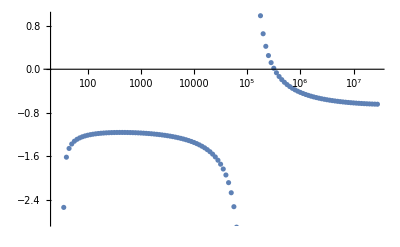

```mathematica
ListLogLinearPlot[SlopesOfLogs]
```

```mathematica
diffSol = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(Sol)/.{w->wvalue,ϵ->epsilonvalue}]/.Mass->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
diffSolMultDiff = Transpose[{Table[10^i,{i,0,7.5-0.02,0.01}],Differences[diffSol[[All,2]]]}];
```

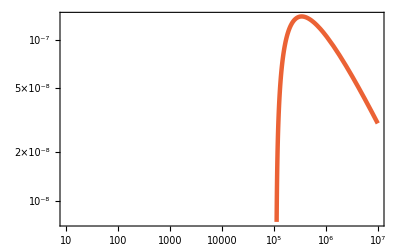

```mathematica
LogLogPlot[(((1/OptPredMass[M])*Psol)/.{M->Mass})/.{w->wvalue,ϵ->epsilonvalue},{Mass,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,4]}]
```

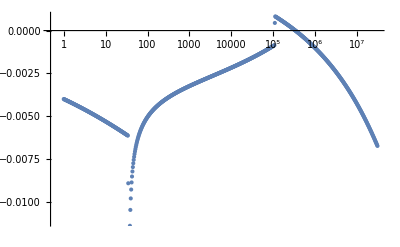

```mathematica
ListLogLinearPlot[diffSol]
```

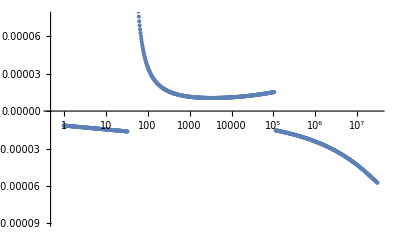

```mathematica
ListLogLinearPlot[diffSolMultDiff]
```

112202.

111605.

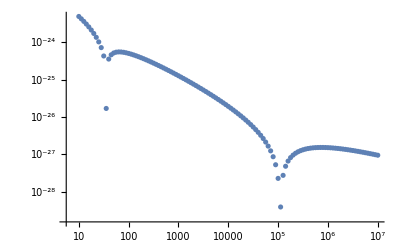

```mathematica
detlist = ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->wvalue,Sub->epsilonvalue}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]
```

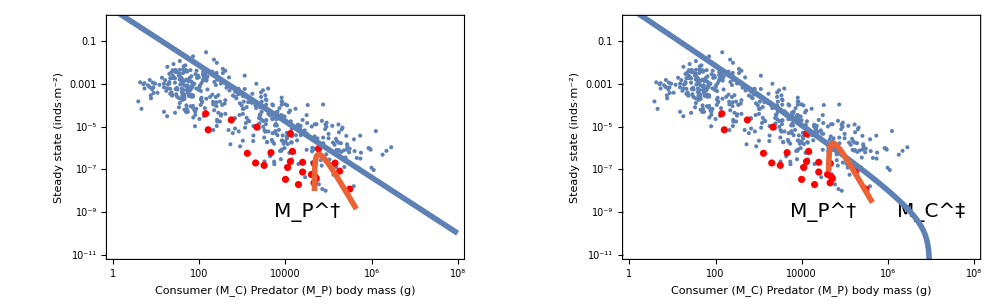

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
PredDensityList=Table[{10^i,((1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.M->10^i},{i,1,8,0.01}];
PredDensityListPredMass = Transpose[{OptPredMass[PredDensityList[[All,1]]],PredDensityList[[All,2]]}];
ThresholdPopulationPlotNoSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
(*LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]*)
ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}]
},ImageSize->800];
ThresholdPopulationPlotNoSubConsSpace=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
(*LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]*)
ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}];
PercentGrowthConsumer=0.5; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
PredDensityList=Table[{10^i,((1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.M->10^i},{i,1,8,0.01}];
PredDensityListPredMass = Transpose[{OptPredMass[PredDensityList[[All,1]]],PredDensityList[[All,2]]}];
ThresholdPopulationPlotSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}],
Graphics[{Text[Style["M_C^‡",FontSize->20],{Log@(10^7),Log@(10^(-9))}]}]
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
(*LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]*)
ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}],
Graphics[{Text[Style["M_C^‡",FontSize->20],{Log@(10^7),Log@(10^(-9))}]}]
}]
},ImageSize->800];
ThresholdPopulationPlotSubPredSpace=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
(*LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]*)
ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}],
Graphics[{Text[Style["M_C^‡",FontSize->20],{Log@(10^7),Log@(10^(-9))}]}]
}];
ThresholdPopulationPlotComb=GraphicsRow[{ThresholdPopulationPlotNoSubConsSpace,ThresholdPopulationPlotSubPredSpace},ImageSize->1000]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb_preypersp.pdf"}],ThresholdPopulationPlotComb,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb_preypersp.pdf

What is the slope of the consumer density?

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.01;
ConsDensityListConsMass=Table[{10^i,((1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.M->10^i},{i,1,8,0.01}];
PredDensityList=Table[{10^i,((1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.M->10^i},{i,1,8,0.01}];
PredDensityListPredMass = Transpose[{OptPredMass[PredDensityList[[All,1]]],PredDensityList[[All,2]]}];
CdensRealPos=Flatten[Position[Table[RealQ[Log@ConsDensityListConsMass[[i,2]]],{i,1,Length[ConsDensityListConsMass[[All,2]]]}],True],1];
Cdenslm =LinearModelFit[Log@(ConsDensityListConsMass[[CdensRealPos]]),x,x];
lmparams=Cdenslm["BestFitParameters"]
```

{1.11268,-1.30945}